

```mathematica
ResourceFunction["DarkMode"][False]
Graph[{1<->2,2<->3,3<->1}]
```

```mathematica
tampa = GeoBoundsRegion[{{28.0600,28.0900},{-82.4843, -82.4481}}]
```

GeoBoundsRegion[{{28.06,28.09},{-82.4843,-82.4481}}]

```mathematica
myRegion = GeoGraphics[tampa]
```

-Graphics-

```mathematica
osm["Ways"][[1]]["Nodes"]
```

{3015057383,97745563,97745561}

```mathematica
allRoads = Table[osm["Nodes", #, "Position"]&/@osm["Ways"][[i]]["Nodes"], {i, Length[osm["Ways"]]}]
```

```mathematica
Length[osm["Ways"]]
```

7672

```mathematica
getPathNodeSet[id_]:=
osm["Nodes", #, "Position"]&/@osm["Ways"][[id]]["Nodes"]
```

```mathematica
getPathNodeSet[28]
```

{GeoPosition[{28.079,-82.4631}],GeoPosition[{28.0786,-82.463}]}

```mathematica
Gather[Flatten[{getPathNodeSet[26], getPathNodeSet[28]}]]
```

{{GeoPosition[{28.0786,-82.4634}]},{GeoPosition[{28.0786,-82.463}],GeoPosition[{28.0786,-82.463}]},{GeoPosition[{28.0785,-82.4625}]},{GeoPosition[{28.0785,-82.4622}]},{GeoPosition[{28.0785,-82.4615}]},{GeoPosition[{28.0783,-82.4615}]},{GeoPosition[{28.079,-82.4631}]}}

```mathematica
findIntersections[st_]:=
First/@Select[Gather[Flatten[getPathNodeSet/@st]], Length[#]>1&]

findNodes[st_]:=DeleteDuplicates[Flatten[{findIntersections[st], First[getPathNodeSet[#]]&/@st, Last[getPathNodeSet[#]]&/@st}]]

findIntersections[Table[i, {i, 26, 36}]]
nodes = findNodes[Table[i, {i, 26, 36}]]
```

{GeoPosition[{28.0786,-82.463}],GeoPosition[{28.0783,-82.4615}]}

{GeoPosition[{28.0786,-82.463}],GeoPosition[{28.0783,-82.4615}],GeoPosition[{28.0786,-82.4634}],GeoPosition[{28.0789,-82.4604}],GeoPosition[{28.079,-82.4631}],GeoPosition[{28.0693,-82.4593}],GeoPosition[{28.0713,-82.4707}],GeoPosition[{28.0726,-82.4605}],GeoPosition[{28.0717,-82.4634}],GeoPosition[{28.0612,-82.4594}],GeoPosition[{28.0638,-82.4543}],GeoPosition[{28.0634,-82.449}],GeoPosition[{28.0777,-82.4634}],GeoPosition[{28.0692,-82.4557}],GeoPosition[{28.0705,-82.4701}],GeoPosition[{28.0727,-82.4633}],GeoPosition[{28.0717,-82.4613}],GeoPosition[{28.0612,-82.4596}],GeoPosition[{28.0638,-82.4511}],GeoPosition[{28.0634,-82.4511}]}

```mathematica
GeoGraphics[Values[Line[Values[osm[["Nodes",#Nodes,"Position"]]]]&/@osm["Ways"][[26;;66]]]]

GeoListPlot[findIntersections[Table[i, {i, 26, 66}]]]

moo = GeoListPlot[findNodes[Table[i, {i, 26, 66}]]]
ImageDimensions[GeoListPlot[findNodes[Table[i, {i, 26, 66}]]]]
```

-Graphics-

-Graphics-

-Graphics-

{840,645}

```mathematica
findEdges[st_]:=
Module[{nodes = findNodes[st]},
Flatten[Table[
fullPath = getPathNodeSet[st[[i]]];
tmp = Select[fullPath, MemberQ[nodes, #]&];
Table[UndirectedEdge[tmp[[j]], tmp[[j+1]], GeoDistance[tmp[[j]], tmp[[j+1]]]], {j, 1, Length[tmp]-1}]

,{i, 1, Length[st]}]]
]

findEdges[Table[i, {i, 26, 26}]]
```

{GeoPosition[{28.0786,-82.4634}]GeoPosition[{28.0783,-82.4615}]621.915 ft}

Viz: 26 to 66

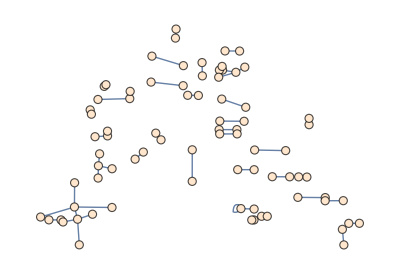

-Graphics-

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
myNodes = findNodes[Table[i, {i, 26, 66}]];
myEdges = findEdges[Table[i, {i, 26, 66}]];
myGraph = Graph[myNodes, myEdges, VertexStyle->LightOrange, (*VertexLabels-> Table[myNodes[[i]]->i, {i, 1, Length[myNodes]}], *)VertexCoordinates->Table[myNodes[[i]]->{1*(myNodes[[i]][[1]][[2]]+82.4654),1*(myNodes[[i]][[1]][[1]]-29.2665)}, {i, 1, Length[myNodes]}]]
eee = RemoveBackground[ImageResize[GraphPlot[myGraph], {815, 645}]]
```

```mathematica
ImageCompose[moo,eee]
```

-Graphics-

get coordinates of each point on the map (pixel)
use vertex coordinates
image size the same
overlay image (show, imagecompose?)

{GeoPosition[{28.0626,-82.4758}],GeoPosition[{28.0627,-82.4801}],GeoPosition[{28.0613,-82.4798}],GeoPosition[{28.061,-82.4815}]}

{GeoPosition[{28.0626,-82.4758}]<->GeoPosition[{28.0627,-82.4801}],GeoPosition[{28.0627,-82.4801}]<->GeoPosition[{28.0613,-82.4798}],GeoPosition[{28.0613,-82.4798}]<->GeoPosition[{28.061,-82.4815}]}

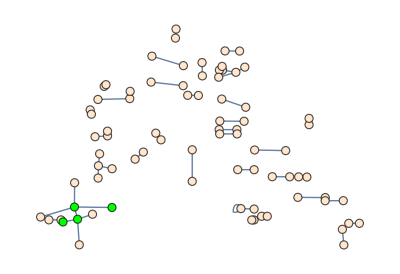

```mathematica
foundPath = Flatten[findLengthKPath[3, myNodes[[47]], myGraph]]
wendyo = makePath[foundPath]
HighlightGraph[myGraph, Style[PathGraph[foundPath], Green]]
```

```mathematica
toad3 = TravelDirections[foundPath]
toad3["TravelPath"]

GeoGraphics[{Red, toad3["TravelPath"]}]
```

TravelDirectionsData[…]

GeoPath[GeoPosition[…],TravelPath]

-Graphics-

```mathematica
fullNodes = findNodes[Table[i, {i, 1, 7672}]];
fullEdges = findEdges[Table[i, {i, 1, 7672}]];
fullGraph = Graph[fullNodes, fullEdges, VertexStyle->LightOrange, (*VertexLabels-> Table[myNodes[[i]]->i, {i, 1, Length[myNodes]}], *)VertexCoordinates->Table[fullNodes[[i]]->{1*(fullNodes[[i]][[1]][[2]]+82.4654),1*(fullNodes[[i]][[1]][[1]]-29.2665)}, {i, 1, Length[fullNodes]}]]
```

```mathematica
foundCycle = Flatten[findLengthKCycle[8, fullNodes[[49]], fullGraph]]
fondCycle = flattenCycle[foundCycle]
HighlightGraph[fullGraph, Style[PathGraph[foundCycle], Green]]

toad4 = TravelDirections[fondCycle]
toad4["TravelPath"]

GeoGraphics[{Red, toad4["TravelPath"]}]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

Part::partw: Part 1 of {} does not exist.

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

{{}⟦1⟧,1⟦1⟧,1⟦2⟧}

TravelDirections::arginvll: At least one of the elements in the list {{}⟦1⟧,1⟦1⟧,1⟦2⟧} is not a valid location.

TravelDirections[{{}⟦1⟧,1⟦1⟧,1⟦2⟧}]

TravelDirections[{{}⟦1⟧,1⟦1⟧,1⟦2⟧}][TravelPath]

-Graphics-

```mathematica
GeoPosition[{0,0}]⟦1⟧
```

{0,0}

```mathematica
tt = GeoPosition[{28.08026,-82.452385}]GeoPosition[{28.080637,-82.452391}]Quantity[137.0852505912384, "Feet"]
```

GeoPosition[{28.0803,-82.4524}]GeoPosition[{28.0806,-82.4524}]137.085 ft

```mathematica
tt[[3]]
```

137.085 ft

```mathematica
GeoGraphics[Values[Line[Values[osm[["Nodes",#Nodes,"Position"]]]]&/@osm["Ways"]]]
```

-Graphics-

```mathematica
osm=ResourceFunction["OSMImport"][GeoBoundsRegion[{{28.0600,28.0900},{-82.4843, -82.4481}}]]
```

```mathematica
osm2 = ResourceFunction["OSMImport"][GeoBoundsRegion[{{45.0600,45.0900},{-93.2943, -93.2621}}]]
```

XML`Parser`XMLGet::prserr: Invalid character in attribute value (Unicode: 0xv) at Line: 64272 Character: 25 in C:\Users\isaia\AppData\Local\Temp\m-235967de-14bb-4a08-a04c-ad7d7b3e9d35\map.osm.

Import::fmterr: Cannot import data as XML format.

Part::partw: Part 1 of {} does not exist.

<|Nodes→<||>,Ways→<||>|>

```mathematica
Keys[osm]
```

{Nodes,Ways}

```mathematica
Head[osm]
```

Association

```mathematica
GeoGraphics[Values[Line[Values[osm[["Nodes",#Nodes,"Position"]]]]&/@Select[osm["Ways"],KeyExistsQ[#Tags,"footway"]&]]]
```

-Graphics-

```mathematica
GeoGraphics[Values[Line[Values[osm[["Nodes",#Nodes,"Position"]]]]&/@Select[osm["Ways"],MatchQ[#[["Tags","highway"]],"sidewalk" | "path" | "footway" | "crosswalk"]&]]]
```

-Graphics-

```mathematica
GeoGraphics[Values[Line[Values[osm[["Nodes",#Nodes,"Position"]]]]&/@Select[osm["Ways"],MatchQ[#[["Tags","highway"]],"primary"|"secondary" | "tertiary" | "residential"]&]]]
```

-Graphics-

```mathematica
RepeatedTiming[Table[i, {i, 1, 100000000}] // Shallow]
```

{2.13549,{1,2,3,4,5,6,7,8,9,10,«99999990»}}

```mathematica
$RecursionLimit = 1000000
```

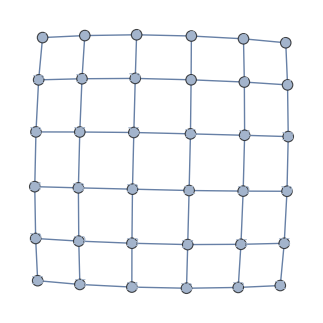

```mathematica
squareGraph[n_Integer]:=
Graph[Flatten[{Table[Table[i*n+j<-> i*n+j+1, {j, 1, n-1}], {i, 0, n-1}], Table[Table[i*n+j<-> i*n+j+n, {j, 1, n}], {i, 0, n-2}]}], VertexLabels->Placed[Automatic,Center],VertexSize->.25, EdgeWeight->{_->1}];
(*squareGraph[n_Integer]:=
Graph[Flatten[{Table[Table[{i*n+j-> i*n+j+1, i*n+j+1-> i*n+j}, {j, 1, n-1}], {i, 0, n-1}], Table[Table[{i*n+j-> i*n+j+n, i*n+j+n-> i*n+j}, {j, 1, n}], {i, 0, n-2}]}], VertexLabels->Placed[Automatic,Center],VertexSize->.75];*)

myGraph = squareGraph[6]
```

```mathematica
ResourceFunction["DepthFirstSearch"][myGraph,1,3]
```

{}

{}

{}

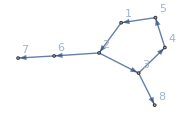

```mathematica
(*Create an undirected cyclic graph*)graph=Graph[{1->2,2->3,3->4,4->5,2->6,6->7,3->8,5->1},VertexLabels->"Name"];

(*Perform a depth-first search starting from node 1 with a maximum depth of 3*)
result=ResourceFunction["DepthFirstSearch"][graph,1,3]

(*Output the result*)
result

(*Highlight the depth-first search path on the graph*)
HighlightGraph[graph,PathGraph[result]]
```

```mathematica
boston = GeoGraphics[GeoBoundsRegion[{{28.0600,28.0900},{-82.4843, -82.4521}}]]
```

```mathematica
atl = GeoBoundsRegion[{{33.7501,33.7901},{-90.3543, -90.3101}}]
Head[atl]
atlanta = GeoGraphics[atl]
```

GeoBoundsRegion[{{33.7501,33.7901},{-90.3543,-90.3101}}]

GeoBoundsRegion

-Graphics-

```mathematica
osmAtlanta=ResourceFunction["OSMImport"][atl]
```

```mathematica
GeoGraphics[Values[Line[Values[osmAtlanta[["Nodes",#Nodes,"Position"]]]]&/@Select[osmAtlanta["Ways"],KeyExistsQ[#Tags,"highway"]&]]]
```

-Graphics-

```mathematica
makePath[lst_]:=
Table[lst[[i]]<->lst[[i+1]], {i, 1, Length[lst]-1}]
```

```mathematica
flattenCycle[lst_]:=
Join[Table[lst[[i]][[1]], {i, 1, Length[lst]}], {Last[lst][[2]]}]
```

```mathematica
findLengthKPath[k_, st_, g_]:=
Module[{rando := RandomSample[Range[VertexCount[g]]]},
candidatePaths = Table[FindPath[g, st, VertexList[g][[rando[[i]]]], {k-5, k+5}], {i, 1, VertexCount[g]}];
Select[candidatePaths, Length[#]>0&, 1]
]
```

```mathematica
findLengthKCycle[k_, st_, g_]:=
Module[{rando := RandomSample[FindCycle[{g, st}, {k-5, k+5}, All]]},
rando[[1]]
]
```

{1,2,3,4,5,6,12,11,10,9,15}

```mathematica
Head[foundPath]
```

List

{16,15,21,22}

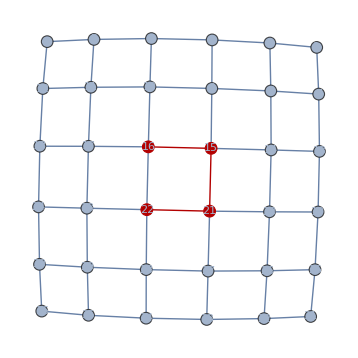

```mathematica
foundPath = Flatten[findLengthKPath[3, 16]]
HighlightGraph[myGraph, PathGraph[foundPath]]
```

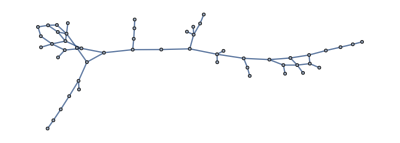

```mathematica
randomG = Graph[{1<->2,2<->3,3<->4, 4<->5, 5<->6, 6<->7, 6<->9, 5<->8, 8<->9, 9<->10, 8<->11, 11<->12, 9<->12, 12<->13, 11<->14, 14<->15, 15<->16, 14<->17, 17<->18, 17<->19, 17<->20, 20<->21, 21<->22, 21<->23, 21<->24, 24<->25, 20<->26, 26<->27, 27<->28, 28<->29, 29<->30, 27<->31, 31<->32, 32<->33, 33<->34, 33<->35, 35<->36, 36<->37, 37<->38, 31<->39, 32<->40, 39<->40, 40<->41, 41<->42, 39<->42, 42<->43, 43<->44, 39<->44, 44<->45, 43<->46, 43<->47, 47<->48, 48<->49, 49<->50, 42<->50, 41<->50, 49<->51, 41<->51, 41<->52}]
```

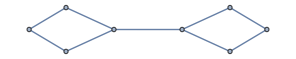

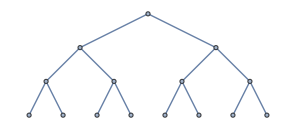

```mathematica
simpleG1 = Graph[{1<->2, 1<->3, 2<->4, 3<->4, 4<->5, 5<->6, 5<->7, 6<->8, 7<->8}]
simpleG2 = Graph[Flatten[Table[{i<->2*i, i<->2*i+1}, {i, 1, 7}]]]
```

```mathematica
Clear[foundPath]
```

{1,2,3,4,5,6,9,8,11,14,17,20,26,27,31,32,40,41,42,39,44,43}

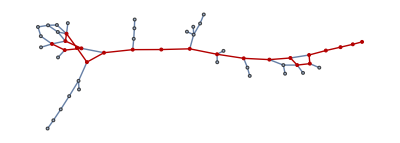

```mathematica
foundPath = Flatten[findLengthKPath[21, 1, randomG]]
HighlightGraph[randomG, PathGraph[foundPath]]
```

```mathematica
FindCycle[{myGraph, 1}, {16}, All]
```

{48<->47,47<->43,43<->42,42<->39,39<->31,31<->32,32<->40,40<->41,41<->51,51<->49,49<->48}

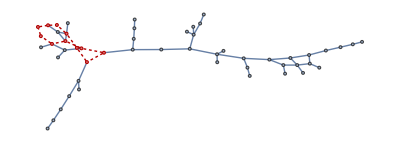

GeoGraphPlot::ngeoedges: {GeoPosition[{500,-300}],GeoPosition[{501,-301}]} is not a list of geo edges

```mathematica
foundCycle = findLengthKCycle[11, 48, randomG]
HighlightGraph[randomG, PathGraph[foundCycle], GraphHighlightStyle->"Dotted"]
```

```mathematica
GeoGraphPlot[{GeoPosition[{50,60.1}]<->GeoPosition[{50.125,59.1}]}, GraphLayout->"Walking"]
```

-Graphics-

```mathematica
GeoGraphPlot[{Entity["Building","TheLouvre::vqy3g"]<->Entity["Building","EiffelTower::5h9w8"]}, GraphLayout->"Walking"]
```

-Graphics-

```mathematica
GeoGraphPlot[{]<->Entity["Building","EiffelTower::5h9w8"]}, GraphLayout->"Walking"]
```

```mathematica
GeoGraphics[Values[Line[Values[osm[["Nodes",#Nodes,"Position"]]]]&/@Select[osm["Ways"],#[["Tags","power"]]==="line"&]]]
```

-Graphics-

TravelDirectionsData[…]

GeoPath[GeoPosition[…],TravelPath]

```mathematica
nodeSet = {GeoPosition[{28.0667, -82.4826}], GeoPosition[{28.0599, -82.4758}]}
GeoGraphPlot[{nodeSet[[1]]<->nodeSet[[2]]}, GraphLayout->"Walking"]

toad1 = TravelDirections[nodeSet]
toad1["TravelPath"]

GeoGraphics[{Red, toad1["TravelPath"]}]
```

{GeoPosition[{28.0667,-82.4826}],GeoPosition[{28.0599,-82.4758}]}

-Graphics-

TravelDirectionsData[…]

GeoPath[GeoPosition[…],TravelPath]

-Graphics-

```mathematica
nodeSet2 = {GeoPosition[{28.0675, -82.4762}], GeoPosition[{28.0676, -82.4758}]}
GeoGraphPlot[{nodeSet2[[1]]<->nodeSet2[[2]]}, GraphLayout->"Walking"]
```

{GeoPosition[{28.0675,-82.4762}],GeoPosition[{28.0676,-82.4758}]}

-Graphics-

```mathematica
toad2 = TravelDirections[nodeSet2, TravelMethod->"Walking"]
toad2["TravelPath"]
```

TravelDirectionsData[…]

GeoPath[GeoPosition[…],TravelPath]

```mathematica
GeoGraphics[{Cyan, toad2["TravelPath"]}]
```

-Graphics-

```mathematica
trafficSignals=Select[osm["Nodes"],MatchQ[#[["Tags","highway"]],"traffic_signals"]&];
positions=Lookup[#,"Position"]&/@trafficSignals;
```

```mathematica
GeoGraphics[Point/@positions]
```

-Graphics-

#### To-learn theory

- That Stanford fixed-length cycle paper
- ?Short cycles on planar graphs: https://www.mimuw.edu.pl/~kowalik/papers/cycles.pdf
- Euler: https://theory.stanford.edu/~virgi/cs267/papers/cycles-ayz.pdf 
- Cycle Basis??
- Misc: https://hackmd.io/6KM0l_nqRJmNFTH8J3_HCQ